```mathematica
(*Define a matrix with a rule f(i, j) with i between a and b and j between c and d:
Table[f(i, j), {i, a, b}, {j, c, d}]*)
```

```mathematica
A = Table[2^(i + j),{i, 0, 3}, {j, 0, 4}]
```

{{1,2,4,8,16},{2,4,8,16,32},{4,8,16,32,64},{8,16,32,64,128}}

```mathematica
MatrixForm[A]
```

(1 | 2 | 4 | 8 | 16
2 | 4 | 8 | 16 | 32
4 | 8 | 16 | 32 | 64
8 | 16 | 32 | 64 | 128)

```mathematica
(*Vandermonde matrix*)
```

```mathematica
n = 3;
A = Table[2^(i + j),{i, 0, n}, {j, 0, n}];
Do[x[i] = -1 + 2i / n, {i, 0, n}];
B = Table[x[i]^j, {i, 0, n}, {j, 0, n}];
MatrixForm[B]
MatrixForm[A.B]
```

(1 | -1 | 1 | -1
1 | -1/3 | 1/9 | -1/27
1 | 1/3 | 1/9 | 1/27
1 | 1 | 1 | 1)

(15 | 23/3 | 29/3 | 191/27
30 | 46/3 | 58/3 | 382/27
60 | 92/3 | 116/3 | 764/27
120 | 184/3 | 232/3 | 1528/27)

```mathematica
(*Inverse of a matrix A:
Inverse[A]*)
```

```mathematica
Inverse[B]
```

{{-1/16,9/16,9/16,-1/16},{1/16,-27/16,27/16,-1/16},{9/16,-9/16,-9/16,9/16},{-9/16,27/16,-27/16,9/16}}

```mathematica
N[Inverse[B].B];
MatrixForm[%]
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.)

```mathematica
(*Transpose of a matrix A:
Transpose[A]*)
```

```mathematica
Transpose[B];
MatrixForm[%]
```

(1 | 1 | 1 | 1
-1 | -1/3 | 1/3 | 1
1 | 1/9 | 1/9 | 1
-1 | -1/27 | 1/27 | 1)

```mathematica
(*Bisection Method using Do*)
```

x=0.5       f[s]=0.332273

x=0.75       f[s]=0.00829652

x=0.875       f[s]=-0.197332

x=0.8125       f[s]=-0.0895985

x=0.78125       f[s]=-0.0395759

x=0.765625       f[s]=-0.0153865

x=0.757813       f[s]=-0.00348347

x=0.753906       f[s]=0.0024217

x=0.755859       f[s]=-0.000527068

x=0.754883       f[s]=0.000948266

x=0.755371       f[s]=0.000210838

x=0.755615       f[s]=-0.000158056

x=0.755493       f[s]=0.0000264058

x=0.755554       f[s]=-0.0000658212

x=0.755524       f[s]=-0.0000197067

x=0.755508       f[s]=3.3498×10^-6

x=0.755516       f[s]=-8.17841×10^-6

x=0.755512       f[s]=-2.41429×10^-6

x=0.75551       f[s]=4.67756×10^-7

x=0.755511       f[s]=-9.73267×10^-7

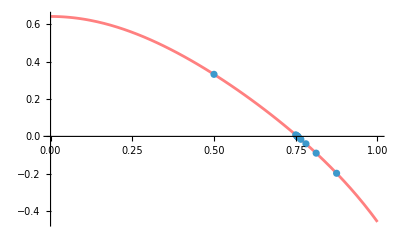

```mathematica
f[x_] = 1/Tan[1 + x^2];
p = Plot[f[x], {x, 0, 1}, PlotStyle->Pink];
a = 0; b = 1;
lis = {};
Do[
s = N[(a + b)/2];
If[f[s]*f[a] < 0, b=s, a = s];
lis = Append[lis, {s, f[s]}];
Print["x=", s, "       ", "f[s]=", f[s]], 
{i, 1, 20}
]
q = ListPlot[lis];
Show[p, q]
```

```mathematica
(*Bisection Method using While*)
```

x=0.5       f[s]=0.332273

x=0.75       f[s]=0.00829652

x=0.875       f[s]=-0.197332

x=0.8125       f[s]=-0.0895985

x=0.78125       f[s]=-0.0395759

x=0.765625       f[s]=-0.0153865

x=0.757813       f[s]=-0.00348347

x=0.753906       f[s]=0.0024217

x=0.755859       f[s]=-0.000527068

x=0.754883       f[s]=0.000948266

x=0.755371       f[s]=0.000210838

x=0.755615       f[s]=-0.000158056

x=0.755493       f[s]=0.0000264058

x=0.755554       f[s]=-0.0000658212

x=0.755524       f[s]=-0.0000197067

x=0.755508       f[s]=3.3498×10^-6

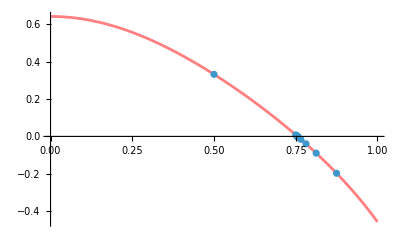

```mathematica
f[x_] = 1/Tan[1 + x^2];
p = Plot[f[x], {x, 0, 1}, PlotStyle->Pink];
a = 0; b = 1;
lis = {};
s = (a+b)/2;
While[Abs[f[s]] > .00001,
s = N[(a + b)/2];
If[f[s]*f[a] < 0, b=s, a = s];
lis = Append[lis, {s, f[s]}];
Print["x=", s, "       ", "f[s]=", f[s]]
]
q = ListPlot[lis];
Show[p, q]
```